```mathematica
X1  = {X,Y,Z};
```

```mathematica
X2 = {x,y,z};
```

```mathematica
RotatedX = EulerMatrix[{α,β,γ}].X2
```

{z Cos[α] Sin[β]+y (-Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ])+x (Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ]),z Sin[α] Sin[β]+x (Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ])+y (Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ]),z Cos[β]-x Cos[γ] Sin[β]+y Sin[β] Sin[γ]}

```mathematica
eq = {X1[[1]]==RotatedX[[1]],X1[[2]]==RotatedX[[2]],X1[[3]]==RotatedX[[3]]} //Simplify
```

{X+y Cos[γ] Sin[α]+x Sin[α] Sin[γ]==Cos[α] (z Sin[β]+Cos[β] (x Cos[γ]-y Sin[γ])),Y==z Sin[α] Sin[β]+Cos[α] (y Cos[γ]+x Sin[γ])+Cos[β] Sin[α] (x Cos[γ]-y Sin[γ]),Z+x Cos[γ] Sin[β]==z Cos[β]+y Sin[β] Sin[γ]}

```mathematica
eq[[1]]
eq[[2]]
eq[[3]]
```

X+y Cos[γ] Sin[α]+x Sin[α] Sin[γ]==Cos[α] (z Sin[β]+Cos[β] (x Cos[γ]-y Sin[γ]))

Y==z Sin[α] Sin[β]+Cos[α] (y Cos[γ]+x Sin[γ])+Cos[β] Sin[α] (x Cos[γ]-y Sin[γ])

Z+x Cos[γ] Sin[β]==z Cos[β]+y Sin[β] Sin[γ]

```mathematica
Solve[eq,{α,β,γ}]
```

{}

```mathematica
EulerMatrix[{α,β,γ}]//MatrixForm
```

(Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ] | -Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ] | Cos[α] Sin[β]
Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ] | Sin[α] Sin[β]
-Cos[γ] Sin[β] | Sin[β] Sin[γ] | Cos[β])

```mathematica
Jeq = {Sin[θJN]Cos[ϕJN],Sin[θJN]Sin[ϕJN],Cos[θJN]};
JSF = {Sin[θJNSF]Cos[ϕJNSF],Sin[θJNSF]Sin[ϕJNSF],Cos[θJNSF]};
```

```mathematica
v = Cross[Jeq,JSF]//Simplify
```

{Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF],-Cos[θJNSF] Cos[ϕJN] Sin[θJN]+Cos[θJN] Cos[ϕJNSF] Sin[θJNSF],-Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF]}

```mathematica
s = √(v.v)//Simplify
```

√(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))

```mathematica
c = Jeq.JSF//Simplify
```

Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]

```mathematica
V = {{0,-v[[3]],v[[2]]},{v[[3]],0,-v[[1]]},{-v[[2]],v[[1]],0}}
```

{{0,Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF],-Cos[θJNSF] Cos[ϕJN] Sin[θJN]+Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]},{-Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF],0,-Cos[θJNSF] Sin[θJN] Sin[ϕJN]+Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]},{Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF],Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF],0}}

```mathematica
R = IdentityMatrix[3]+V + V.V(1-c)/s^2//FullSimplify
```

{{1+((-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) ((Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF])^2+Sin[θJN]^2 Sin[θJNSF]^2 Sin[ϕJN-ϕJNSF]^2))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF]+((Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),-Cos[θJNSF] Cos[ϕJN] Sin[θJN]+Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]+(Sin[θJN] Sin[θJNSF] (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF] (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))},{-Sin[θJN] Sin[θJNSF] Sin[ϕJN-ϕJNSF]+((Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),1+((-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) (Cos[θJNSF]^2 Sin[θJN]^2 Sin[ϕJN]^2-2 Cos[θJN] Cos[θJNSF] Sin[θJN] Sin[θJNSF] Sin[ϕJN] Sin[ϕJNSF]+Sin[θJNSF]^2 (Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2+Cos[θJN]^2 Sin[ϕJNSF]^2)))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),-Cos[θJNSF] Sin[θJN] Sin[ϕJN]-(Sin[θJN] Sin[θJNSF] (Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF])/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))+Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]},{Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]+(Sin[θJN] Sin[θJNSF] (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF] (Cos[θJNSF] Sin[θJN] Sin[ϕJN]-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF]))/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2)),Cos[θJNSF] Sin[θJN] Sin[ϕJN]-(Sin[θJN] Sin[θJNSF] (Cos[θJNSF] Cos[ϕJN] Sin[θJN]-Cos[θJN] Cos[ϕJNSF] Sin[θJNSF]) (-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF]) Sin[ϕJN-ϕJNSF])/(Cos[θJNSF]^2 Sin[θJN]^2-Cos[θJNSF] Cos[ϕJN-ϕJNSF] Sin[2 θJN] Sin[θJNSF]+Sin[θJNSF]^2 (Cos[θJN]^2+Sin[θJN]^2 Sin[ϕJN-ϕJNSF]^2))-Cos[θJN] Sin[θJNSF] Sin[ϕJNSF],1+(-1+Cos[θJN] Cos[θJNSF]+Cos[ϕJN-ϕJNSF] Sin[θJN] Sin[θJNSF])/(1+Sin[ϕJN-ϕJNSF]/(-2 Cot[θJN] Cot[θJNSF] Cot[ϕJN-ϕJNSF]+(Cot[θJN]^2+Cot[θJNSF]^2) Csc[ϕJN-ϕJNSF]))}}

```mathematica
Assumptions-> {ι∈ {0,2π},A∈ Re, B∈Re, c∈Re, d∈Re}
```

Assumptions→{ι∈{0,2 π},A∈Re,B∈Re,c∈Re,d∈Re}

```mathematica
sols =Simplify[Solve[Sin[ι]A + Sin[ι]B + Cos[ι] c == Cos[θ],Sin[theta]^2 == Cross[J,n].Cross[J,n],{ι}],Assumptions->{C[1]∈ Integers}]
```

Solve[Cos[θ]==c Cos[ι]+(A+B) Sin[ι],Sin[theta]^2==(A-B)^2 Sin[ι]^2+(A Cos[ι]-c Sin[ι])^2+(B Cos[ι]-c Sin[ι])^2,{ι}]

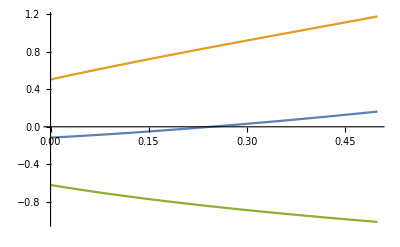

```mathematica
Plot[{ι/.sols[[1]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0,ι/.sols[[2]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0,(ι/.sols[[1]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0 )-(ι/.sols[[2]]/.c->√(1-A^2+B^2)/.B->.2/.d->.99/.C[1]->0)},{A,0,.5}]
```

```mathematica
(ι/.sols[[1]]/.c->√(1-A^2+B^2)/.B->.6/.d->.9/.C[1]->0 )-(ι/.sols[[2]]/.c->√(1-A^2+B^2)/.B->.6/.d->.9/.C[1]->0)/.A->.2 //N
```

-1.74515

```mathematica
J = {A,B,c};
n = {Sin[ι], Sin[ι],Cos[ι]};
```

```mathematica
Cross[J,n].Cross[J,n]
```

(A Sin[ι]-B Sin[ι])^2+(B Cos[ι]-c Sin[ι])^2+(-A Cos[ι]+c Sin[ι])^2

```mathematica
Simplify[Solve[Sin[θ]^2== Cross[J,n].Cross[J,n],{ι}],Assumptions->C[1]∈Integers]
```

{{ι→ArcTan[(√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))) (A^2 c^2+2 A B c^2+B^2 c^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))))/((A+B) c (A^2+B^2-Sin[θ]^2)),√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]},{ι→ArcTan[-(√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))) (A^2 c^2+2 A B c^2+B^2 c^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))))/((A+B) c (A^2+B^2-Sin[θ]^2)),-√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]},{ι→ArcTan[((A^2 c^2+2 A B c^2+B^2 c^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))) √((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))))/((A+B) c (A^2+B^2-Sin[θ]^2)),√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]},{ι→ArcTan[-((A^2 c^2+2 A B c^2+B^2 c^2-√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4))) √((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2))))/((A+B) c (A^2+B^2-Sin[θ]^2)),-√((A^3 B+A B^3+2 A B c^2+(-A B+c^2) Sin[θ]^2+√(-(A+B)^2 c^2 ((A-B)^2 (A^2+B^2+c^2)-2 (A^2-A B+B^2+c^2) Sin[θ]^2+Sin[θ]^4)))/((A^2+c^2) (B^2+c^2)))]+2 π C[1]}}